## Cosmology Project

💡 Name : Mohamed Elashri.
💡 ID : 201303846
💡 SN data are taken from http://supernova.lbl.gov/Union/

## Theory

### Settings for the mathematica file

I’ve to Include some packages needed.

```mathematica
Needs["ErrorBarPlots`"]
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Now Set work directory. Modify it to your own directory (just you have to put the path to the folder I sent).

```mathematica
SetDirectory["C:\\Users\\MohamedIBrahim.MohamedIBrahim\\Desktop\\project"];
```

### Conventions, parameters, etc

FRW Metric: ds^2=-dt^2+a[t]^2(dr^2/(1-k r^2)+r^2(dθ^2+Sin[θ]^2 dϕ^2))

Ωm0: matter density
Ωd0: dark energy/cosmological constant density 
Ωr0w: radiation density

```mathematica
Ωm0w=0.3;
Ωd0w=0.7;
Ωr0w=0;
```

## Part 1 - Ditance vs Redshift

### Plot SN data with error bar I’ve used the Supernovae project Cosmology DATA as it is more organized and up to date

#### now I’ve to Import and display “SCPUnion2_AllSNe.tex” file

This Read the data file of SCPUnion2_mu_vs_z.txt

```mathematica
dataunionfulltmp=Import["DATA/UNION2/SCPUnion2_AllSNe.tex","Table"];
```

And this define Length of dataunionfulltmp

```mathematica
lenfull=Length[dataunionfulltmp];
```

Also define the manipulation for table

```mathematica
dataunionfull=Table[{dataunionfulltmp[[i,1]],dataunionfulltmp[[i,3]],dataunionfulltmp[[i,5]],dataunionfulltmp[[i,7]],dataunionfulltmp[[i,9]],dataunionfulltmp[[i,11]],dataunionfulltmp[[i,13]],dataunionfulltmp[[i,15]]},{i,1,lenfull}];
dataunionfulltable=Grid[Join[{{Name,Redshift,Mag,Stetch,Color,Distance,Sample,CutsFails}},dataunionfull], Alignment -> Left, Spacings -> {2, 1}, Frame -> All,ItemStyle->"Text", Background->{{Gray,None},{LightGray,None}}];
```

#### Import and display “SCPUnion2_mu _vs _z _adjust.txt” data file.

now I Import dataunion adjusted data. This data includes name, redshift, distance, error. recpectively (as in the source file)
Data columns are : Name, Redshift , Distance modulus  and uncertinty recpecively

```mathematica
dataunion=Import["DATA/UNION2/SCPUnion2_mu_vs_z_adjust.txt","Table"];
datauniontable=Grid[Join[{{Name,Redshift,Distance,Error}},dataunion], Alignment -> Left, Spacings -> {2, 1}, Frame -> All,ItemStyle->"Text", Background->{{Gray,None},{LightGray,None}}];
```

now to show dataunion table.

```mathematica
datauniontable;
```

calculate the length of this dataunion table

```mathematica
len=Length[dataunion];
```

We can simplify dataunion table and call it du

```mathematica
du=Table[{dataunion[[i,2]],dataunion[[i,3]],dataunion[[i,4]]},{i,1,len}];
dutable=Grid[Join[{{Redshift,Distance,Error}},du], Alignment -> Left, Spacings -> {2, 1}, Frame -> All,ItemStyle->"Text", Background->{{Gray,None},{None,None}}];
```

now if we want to show du table

```mathematica
dutable;
```

#### Plotting the Distance-Redshift Diagram .

Plot du table Distance as function of redshift

```mathematica
plunion=ErrorListPlot[du,PlotRange->All];
```

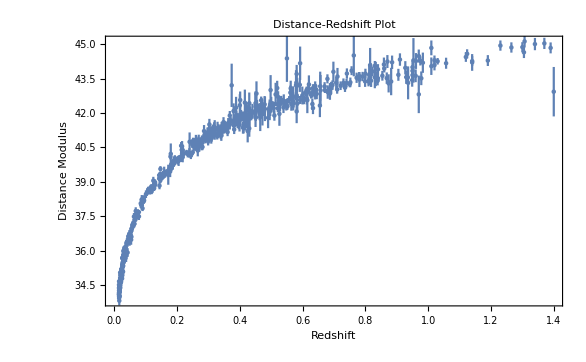

```mathematica
Show[plunion,Frame->True,FrameLabel->{"Redshift","Distance Modulus"},PlotLabel->Style["Distance-Redshift Plot",16,Green]]
```

## Effective magnitude vs Redshift

#### Calculating distance/magniude at different redshift.

to deal with the different curvature value , define a piecewise function

```mathematica
daz[Ωm0_?NumberQ,Ωd0_?NumberQ,Ωk0_?NumberQ,z_?NumberQ]:=Piecewise[{{c/H0(1+z)1/(√Ωk0)Sinh[√Ωk0 NIntegrate[1/(√(Ωm0(1+zz)^3+Ωd0+Ωk0(1+zz)^2)),{zz,0,z}]],Ωk0>0},{c/H0(1+z)NIntegrate[1/(√(Ωm0(1+zz)^3+Ωd0)),{zz,0,z}],Ωk0==0},{c/H0(1+z)1/(√-Ωk0)Sin[√-Ωk0 NIntegrate[1/(√(Ωm0(1+zz)^3+Ωd0+Ωk0(1+zz)^2)),{zz,0,z}]],Ωk0<0}}] ;
```

Distance at redshift z

```mathematica
dz[Ωm0_?NumberQ,Ωd0_?NumberQ,Ωk0_?NumberQ,z_?NumberQ]:=(1+z)NIntegrate[1/hubble[Ωm0,Ωd0,Ωk0,tmp],{tmp,0,z}]  ;
```

Magnitude calculated from distance. Theoretically of cause.

```mathematica
mag[Ωm0_?NumberQ,Ωd0_?NumberQ,Ωk0_?NumberQ,z_?NumberQ]:=5Log[10,daz[Ωm0,Ωd0,Ωk0,z]]+25 ;
```

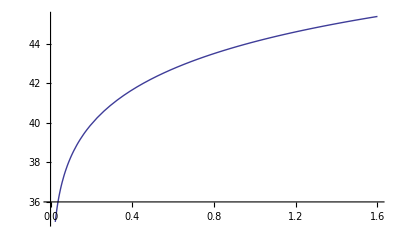

```mathematica
plmagth=Plot[mag[Ωm0,Ωd0,0,z],{z,0,1.6}]
```

```mathematica
plmagth1=Plot[mag[0.3,0.7,0,z],{z,0,1.6}]
```

-Graphics-

```mathematica
plmagth2=Plot[mag[0.3,0,0,z],{z,0,1.6}]
```

-Graphics-

```mathematica
plmagth3=Plot[mag[1,0,0,z],{z,0,1.6}]
```

-Graphics-

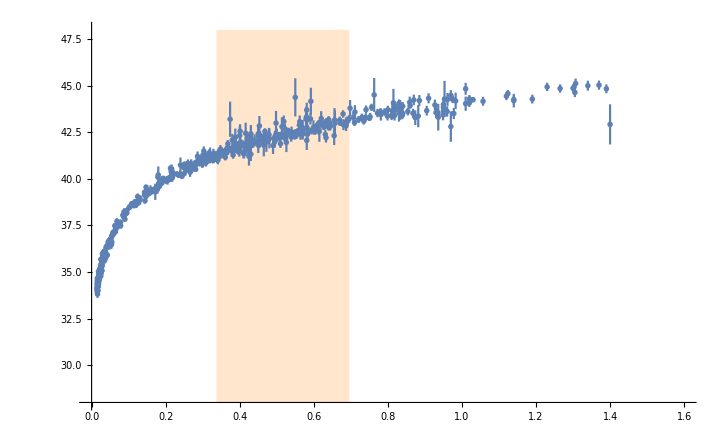

```mathematica
Show[{plunion,plmagth},PlotRange->{{0,1.6},{28,48}},AxesOrigin->{0,28},Prolog->{LightOrange,Rectangle[{0.426-0.089,28},{0.426+0.27,48}]}]
```

## chi square fitting

### chi square fitting. Using mathematica’s functions.

#### Definations etc

chi ^2 defination with error column , which can be found from .SCPUnion2_covmat _sys.txt data file

```mathematica
chi2unionsl[Ωm0_?NumberQ,zt_?NumberQ]:=ParallelSum[(du[[i,2]]-mag[Ωm0,1/2 Ωm0(1+zt)^3,1-Ωm0-1/2 Ωm0(1+zt)^3,du[[i,1]]])^2/du[[i,3]]^2,{i,1,len}]
```

Define a table of  “theory-observation”.

```mathematica
thobtab[Ωm0_,zt_]=ParallelTable[du[[i,2]]-mag[Ωm0,1/2 Ωm0(1+zt)^3,1-Ωm0-1/2 Ωm0(1+zt)^3,du[[i,1]]],{i,1,len}];
```

Import covariance matrix data. “covm” is data with systematic and “covmns” is data without sys.

```mathematica
covm=Import["DATA/UNION2/SCPUnion2_covmat_sys.txt","Table"];
icovm=Inverse[covm];
```

```mathematica
covmns=Import["DATA/UNION2/SCPUnion2_covmat_nosys.txt","Table"];
icovmns=Inverse[covmns];
```

Testing the imported file.

```mathematica
(du[[1]][[3]])^-2
icovmns[[1,1]]
```

19.5538

19.5535

Define chi^2 with and without systematic.

```mathematica
chi2union[Ωm0_?NumberQ,zt_?NumberQ]:=thobtab[Ωm0,zt].icovm.thobtab[Ωm0,zt]
```

```mathematica
chi2unionns[Ωm0_?NumberQ,zt_?NumberQ]:=thobtab[Ωm0,zt].icovmns.thobtab[Ωm0,zt]
```

Test the calcuation speed.

```mathematica
chi2union[0.27,0.5]//Timing
```

{7.176,551.036}

```mathematica
chi2unionns[0.27,0.5]//Timing
```

{7.269,690.772}

```mathematica
chi2unionsl[0.27,0.5]//Timing
```

{0.,690.775}

#### With Systematic in data. Find the minimum of chi2.

```mathematica
Off[FindMinimum::lstol]
chi2mini=FindMinimum[chi2union[x,y],{x,0.15},{y,0.4}]
On[FindMinimum::lstol]
```

```mathematica
Export["OUTPUT\\2\\chi2union_minimum.dat",chi2mini]
```

OUTPUT\2\chi2union_minimum.dat

Plot the contour with confidential level 1σ and 2σ. This is a 2 parameter model. Δχ^2(1σ)=2.30 && Δχ^2(2σ)=6.18 && Δχ^2(3σ)=11.83.

With sys.

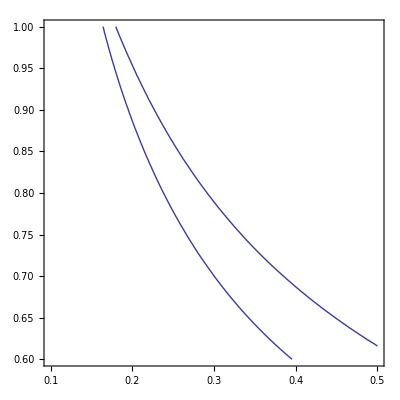

```mathematica
Off[NIntegrate::nlim]
Off[NIntegrate::slwcon]
conchi21s=ContourPlot[{chi2union[Ωm0,zt]==chi2mini[[1]]+2.30},{Ωm0,0.1,0.5},{zt,0.6,1.0}]
On[NIntegrate::nlim]
On[NIntegrate::slwcon]
```

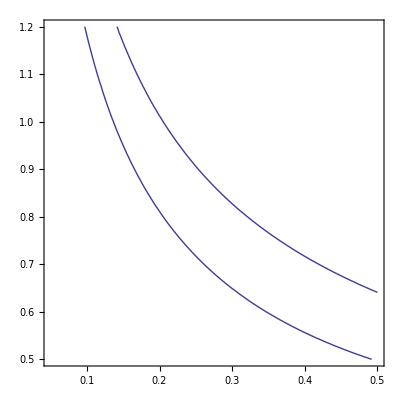

```mathematica
Off[NIntegrate::nlim]
Off[NIntegrate::slwcon]
conchi22s=ContourPlot[{chi2union[Ωm0,zt]==chi2mini[[1]]+6.18},{Ωm0,0.05,0.5},{zt,0.5,1.2}]
On[NIntegrate::nlim]
On[NIntegrate::slwcon]
```

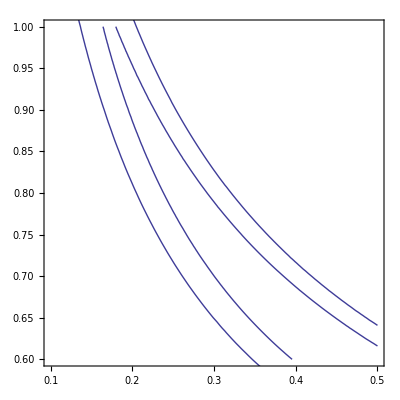

```mathematica
conchi2=Show[conchi21s,conchi22s]
```

```mathematica
Export["OUTPUT\\2\\conchi21s.eps",conchi21s]
Export["OUTPUT\\2\\conchi22s.eps",conchi22s]
Export["OUTPUT\\2\\conchi2.eps",conchi2]
```

OUTPUT\2\conchi21s.eps

OUTPUT\2\conchi22s.eps

OUTPUT\2\conchi2.eps